```mathematica
ω=.
i=.
x=.
n=.
h=.
```

```mathematica
(* EQ 15 *)
gxib=Exp[∑_(i=1)^n β[[i]] x[[i]]];//Quiet
```

```mathematica
(* EQ 19 *)
pixiG=(1-(1-h)^(gxib)) ∏_(k=1)^(i-1) ((1-h)^(gxib));
```

```mathematica
(* EQ 32 *)
lnL=-ω ∑_(i=1)^n ((1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6] Exp[x7[[i]] β7])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5] Exp[x6[[k]] β6] Exp[x7[[k]] β7])))+Log[ω]∑_(i=1)^n (y[[i]] ) + ∑_(i=1)^n (y[[i]] Log[(1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6] Exp[x7[[i]] β7])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5] Exp[x6[[k]] β6] Exp[x7[[k]] β7]))])-∑_(i=1)^n Log[y[[i]]!];//Quiet
```

```mathematica
(* Hazard Functions *)
GM=b;
NB2=(i b^2)/(1+b (i-1));
DW2=1-b^(i^2-(i-1)^2);
DW3=1-Exp[-c i^b];
S=p (1-pi^i);
TL=(1-Exp[-1/d])/(1+Exp[-(i-c)/d]);
IFRSB=1-c/i;
IFRGSB=1-c/((i-1) α+1);
```

```mathematica
(* Covariate data *)
Cov1={0.0531,0.0619,0.158,0.081,1.046,1.75,2.96,4.97,0.42,4.7,0.9,1.5,2,1.2,1.2,2.2,7.6};
Cov2={4,20,1,1,32,32,24,24,24,30,0,8,8,12,20,32,24};
Cov3={1,0,0.5,0.5,2,5,4.5,2.5,4,2,0,4,6,4,6,10,8};
Cov4=RandomReal[] Cov1;
Cov5=RandomReal[] Cov2;
Cov6  =RandomReal[] Cov3;
Cov7 = RandomReal[] Cov1;
```

```mathematica
(* Loop to generate failure counts *)
ω=75;
FC=List[];
For[j=1,j≤17,j++,
i=j;
x={Cov1[[j]],Cov2[[j]],Cov3[[j]],Cov4[[j]],Cov5[[j]],Cov6[[j]],Cov7[[j]]};
FC=Append[FC,Part[RandomVariate[PoissonDistribution[ω pixiG/.{n->7,β->{0.12707767,0.03063154,0.10213574,0.01,0.01,0.01,0.01},h->NB2/.{b->0.08478873}}],1],1]];//Quiet
]
ω=.
FC
n=Length[FC]
```

{1,1,0,2,6,8,1,4,3,0,3,2,2,4,1,0,0}

17

```mathematica
(* Cummulative Failure Count *)
CummulativeFC = List[FC[[1]]];
For[j=2,j≤17,j++,
CummulativeFC=Append[CummulativeFC,FC[[j]]+CummulativeFC[[j-1]]];
]
CummulativeFC
```

{1,2,2,4,10,18,19,23,26,26,29,31,33,37,38,38,38}

```mathematica
(* MLEs *)
h=NB2;
lnLa=lnL/.{y-> FC,x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5,x6->Cov6,x7->Cov7};//Quiet
Rules=FindRoot[{{0==D[lnLa,ω]},{0==D[lnLa,β1]},{0==D[lnLa,β2]},{0==D[lnLa,β3]},{0==D[lnLa,β4]},{0==D[lnLa,β5]},{0==D[lnLa,β6]},{0==D[lnLa,β7]},{0==D[lnLa,b]}},{{ω,55},{β1,0.12707767},{β2,0.03063154},{β3,0.10213574},{β4,0.01},{β5,0.01},{β6,0.01},{β7,0.01},{b,0.08478873}},MaxIterations->100000]
```

{ω→38.4009,β1→-0.053187,β2→-0.0422602,β3→0.306282,β4→0.01,β5→0.0844847,β6→0.01,β7→0.01,b→0.0840902}

```mathematica
(* Model fit *)
j=.
Hω=∑_(i=1)^j ω(1-((1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6] Exp[x7[[i]] β7]))) ∏_(g=1)^(i-1) (1-h)^(Exp[x1[[g]] β1]Exp[x2[[g]] β2]Exp[x3[[g]] β3] Exp[x4[[g]] β4] Exp[x5[[g]] β5]Exp[x6[[g]] β6] Exp[x7[[g]] β7])/.Rules/.{x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5,x6-> Cov6, x7->Cov7};//Quiet
HωList={};
For[k=1,k≤ n,
AppendTo[HωList,Hω/.j->k];
k=k+1;
]; //Quiet
HωList//N
```

{2.75244,4.90608,6.90926,8.79871,12.2536,19.2018,23.2065,24.8499,27.5592,28.6322,29.1143,30.6871,32.9123,33.8826,35.3435,37.6885,38.}

```mathematica
(* Goodness of fit *)
AIC=2 p-2 lnLa/.Rules/.p-> 9
BIC=+ p Log[n]-2 lnLa/.Rules/.p-> 9
SSE=∑_(i=1)^n (HωList[[i]]-CummulativeFC[[i]])^2
```

86.5285

94.0274

112.634

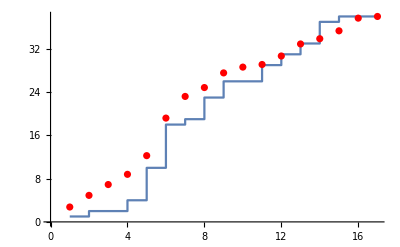

```mathematica
(* Plot data and model fit *)
gEmpirical=ListPlot[CummulativeFC,InterpolationOrder->0,Joined->True];
gFitted=ListPlot[HωList,PlotStyle->Red];(*,Joined->True,InterpolationOrder->4*)
Show[gEmpirical,gFitted]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Caroline\Desktop\covariate simulation\DS1\NB2

```mathematica
Intervals=Table[i,{i,1,17}];
(* NB2 doesn't give consistently good fits, forgo fitness test before export*)
Export["NB2_7cov_sim.xlsx",Transpose[{Intervals,FC,Cov1,Cov2,Cov3, Cov4, Cov5, Cov6, Cov7}]]
```

NB2_7cov_sim.xlsx